# Chapter. Increasing the speed and accuracy of computations

Mathematica preliminaries

```mathematica
If[Length[Names["Global`*"]]>0,Remove["Global`*"]];
```

```mathematica
Off[General::"spell"];
Off[General::"spell1"];
```

```mathematica
SetOptions[EvaluationNotebook[],
PrintingStartingPageNumber->36,

PageHeaders->{
{Cell[TextData[{CounterBox["Page"]}], FontFamily->"Arial",FontSize->12],  Cell[TextData[{"Increasing speed and accuracy"}], FontFamily->"Arial",FontSize->12],None},
{None,Cell[TextData[CounterBox["Section",CounterFunction:>(Part[{"Introduction","Weighted schemes. The Crank-Nicolson method","Higher order approximations","Using space elements with variable dimensions","Summary","Further Reading"},#]&)]], FontFamily->"Arial",FontSize->12],
       Cell[TextData[{CounterBox["Page"]}], FontFamily->"Arial",FontSize->12]}},
PageFooters->{{None,None,None},{None,None,None}},
PrintingOptions-> {
"PrintingMargins"->{{90,90},{60,90}},
"PaperSize"->{596,794},
"PageSize"->{596,794},
"PageHeaderMargins"->{60,60},
"PageFooterMargins"->{30,30},
"FirstPageFace"->Left,
"FirstPageHeader"->False,
"FirstPageFooter"->False,
"PrintRegistrationMarks"-> False}];
```

```mathematica
Needs["Notation`"];
```

```mathematica
ClearNotations[];
Symbolize[Δy];
```

```mathematica
SetOptions[Graphics,
ImageSize->288];
```

```mathematica
SetOptions[Plot,
Axes-> False,
BaseStyle->Directive[FontFamily->"Arial",11,Plain,GrayLevel[0.2]],
Frame->True,
FrameStyle->{Black,AbsoluteThickness[.5]},
GridLines->None,
ImageSize->288,
LabelStyle->Directive[FontFamily->"Arial",11,Plain,GrayLevel[0.2]],
PlotStyle->AbsoluteThickness[.5]];
```

```mathematica
SetOptions[ListPlot,
Axes-> False,
BaseStyle->Directive[FontFamily->"Arial",11,Plain,GrayLevel[0.2]],
Frame->True,
FrameStyle->{Black,AbsoluteThickness[.5]},
GridLines->None,
ImageSize->288,
LabelStyle->Directive[FontFamily->"Arial",11,Plain,GrayLevel[0.2]],
PlotStyle->AbsoluteThickness[.5],
Joined->True];
```

```mathematica
SetOptions[Plot3D,
AspectRatio-> 1,
ImageSize->288,
LabelStyle->Directive[FontFamily->"Arial",11,Plain,GrayLevel[0.2]],
Mesh-> False,
PlotRange->All,
PlotPoints->40];
```

```mathematica
SetOptions[ListPlot3D,
AspectRatio-> 1,
Axes->True,
AxesLabel->{"k","j","  c"},
AxesEdge->{{-1,-1},{1,-1},{1,1}},
AxesStyle->AbsoluteThickness[1],
Boxed-> True,
BoxRatios->{1,1,.7},
BoxStyle->AbsoluteDashing[{2.5,2.5}],
ImageSize->288,
LabelStyle->Directive[FontFamily->"Arial",11,Bold,GrayLevel[0.2]],
Lighting-> Automatic,
Mesh->False,
PlotRange->All,
ViewVertical->{0,0,1},
ViewPoint->{2.2,-1.2,1}];
```

```mathematica
optionA={
Axes-> False,
Frame-> True,
FrameLabel-> {
Style["k",FontFamily-> "Times New Roman",12, Italic],
Style["z",FontFamily-> "Times New Roman",12,Italic],
None,None},
Frame-> False,
Joined-> False,
(*PlotRange:> {{0, n}, {0, -3}},*)
PlotLabel-> None,
PlotStyle-> Thickness[0],
Prolog-> {Black,AbsolutePointSize[4.5]}
};
```

```mathematica
optionB={
Axes-> False,
Frame-> True,
FrameLabel-> {
Style["k",FontFamily-> "Times New Roman",12, Italic],
Style["z",FontFamily-> "Times New Roman",12,Italic],None,None},
Frame-> False,
Joined-> True,
(*PlotRange:>{{0, n}, {0,-3}},*)
PlotRegion-> {{0,1},{0.1,0.9}},
PlotLabel-> None
};
```

```mathematica
ClearAll[makeDiagonals,makeMatrix,implicitSolve];

makeDiagonals[m_Integer,α_]:=
	Module[{x,y,z},
		x=Table[-α,{m-3}];
		z=Table[-α,{m-3}];
		y=Table[1.+2.*α,{m-2}];
{x,y,z}
];

makeMatrix[m_Integer,α_]:=Module[{x,y,z},
{x,y,z}=makeDiagonals[m,α];
Table[Switch[j-i,-1,x⟦j⟧,0,y⟦j⟧,1,z⟦j-1⟧,_,0],{i,m-2},{j,m-2}]
];

implicitSolve[m_Integer,n_Integer,α_]:=Module[{solveNext,mat,lsf,b1},

solveNext[α1_]:=Module[{tmp,b},
tmp=#⟦2;;-2⟧;
b=Flatten[{tmp⟦1;;-2⟧,Last[tmp]+α1}];
Flatten[{0.,lsf[b],1.}]
]&;

mat=makeMatrix[m,α];
lsf=LinearSolve[mat];
b1=Table[1.,{m}];
Transpose@NestList[solveNext[α],b1,n-1]
];
```

```mathematica
$Line=0;
```

Chapter.Section Introduction

The previous chapter introduced explicit and implicit finite difference methods and the implementation of those methods using Mathematica. In this chapter we begin by looking at ways to improve the accuracy of computation by combining the explicit and implicit methods and by using higher order approximations.
Even with the amount of computing power available on desktops these days when grid sizes become large the analysis can become time consuming. This is most noticeable for simulating alternating current electrochemical methods (Chapter 7) where grids with 30000 time steps are typical. The second half of this chapter examines methods to enhance computation speed by incorporating expanding grids.

## Chapter.Section Weighted schemes. The Crank-Nicolson method

In the last chapter we demonstrated how fully explicit and fully implicit methods could be solved within Mathematica. These two methods can be combined to produce a weighted scheme by introducing a weighting factor, θ, in the following fashion

c(j, k+1)-c(j, k)=θ(DΔ t)/(Δx)^2(c(j+1, k+1)-2c(j,k+1)+c(j-1, k+1))+(1-θ)DΔt/(Δx)^2(c(j+1, k)-2c(j,k)+c(j-1, k))

In dimensionless form eqn (Chapter.EquationNumbered) becomes

c_j^(k+1)-c_j^k=θD(c_(j-1)^(k+1)-2 c_j^(k+1)+c_(j+1)^(k+1))+(1-θ)D(c_(j-1)^k-2 c_j^k+c_(j+1)^k)

Rearranging eqn (Chapter.EquationNumbered) to have all the k+1 terms on the left hand side and all the k terms on the right hand side gives

-θD c_(j-1)^(k+1)+(1+2θD)c_j^(k+1)-θD c_(j+1)^(k+1)=(1-θ)D c_(j-1)^k+(1-2(1-θ)D)c_j^k+(1-θ)D c_(j+1)^k

or

-c_(j-1)^(k+1)+(1+2θD)/θD c_j^(k+1)-c_(j+1)^(k+1)=(1-θ)/θ c_(j-1)^k+(1-2(1-θ)D)/θD c_j^k+(1-θ)/θ c_(j+1)^k

When θ=0.5 the method is known as the Crank-Nicolson method (Fig. Chapter.FigureCaption).

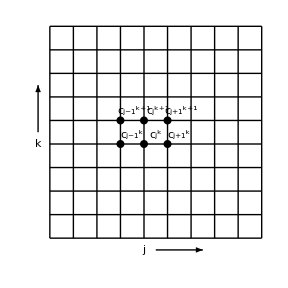

```mathematica
ClearAll[label,vert,horiz,option1,c,k,j];

label[x_]:=DisplayForm[TraditionalForm[MakeBoxes[x,TraditionalForm]]];

(*make vertical and horizontal lines*)
vert=Table[Line[{{i,1},{i,10}}],{i,1,10}];
horiz=Table[Line[{{1,i},{10,i}}],{i,1,10}];

option1={
AspectRatio-> 1,
BaseStyle-> {FontFamily-> "Times New Roman",FontSize-> 14, FontWeight->Plain},
ImagePadding->{{5,5},{5,5}},
Prolog-> {
Text[TraditionalForm[k],{0.5,5.}],
Text[TraditionalForm[j],{5.,0.5}],
Text[label[Subscript[c, j-1]^k],{4.5,5.4}],
Text[label[Subscript[c, j]^k],{5.5,5.4}],
Text[label[Subscript[c, j+1]^k],{6.5,5.4}],
Text[label[Subscript[c, j]^(k+1)],{5.6,6.4}],
Text[label[Subscript[c, j-1]^(k+1)],{4.6,6.4}],
Text[label[Subscript[c, j+1]^(k+1)],{6.6,6.4}],
PointSize[0.02],
Point[{4,5}],
Point[{5,5}],
Point[{6,5}],
Point[{4,6}],
Point[{5,6}],
Point[{6,6}],
Arrowheads[{0,0.03}],
Arrow[{{0.5,5.5},{0.5,7.5}}],
Arrow[{{5.5,0.5},{7.5,0.5}}]
}
};

Graphics[{vert,horiz},PlotRange->{{0,10},{0,10}},option1]
SelectionMove[EvaluationNotebook[],Previous,Cell]
FrontEndExecute[FrontEndToken["OpenCloseGroup"]];
SelectionMove[EvaluationNotebook[],After,Cell]
```

Fig. Chapter.FigureCaption  For the Crank-Nicolson method six concentration points are used for calculations at each step.

In dimensionless form the Crank-Nicolson method is

-c_(j-1)^(k+1)+(2/D+2)c_j^(k+1)-c_(j+1)^(k+1)=c_(j-1)^k+(2/D-2)c_j^k+c_(j+1)^k

which, after moving the boundary values at k+1 to the right hand, kth, side produces to the following system of equations:

(2/D+2)c_2^(k+1)-c_3^(k+1)=c_1^k+(2/D-2)c_2^k+c_3^k+c_1^(k+1)
-c_2^(k+1)+(2/D+2)c_3^(k+1)-c_4^(k+1)=c_2^k+(2/D-2)c_3^k+c_4^k
-c_3^(k+1)+(2/D+2)c_4^(k+1)-c_5^(k+1)=c_3^k+(2/D-2)c_4^k+c_5^k
⋮
-c_(j-1)^(k+1)+(2/D+2)c_j^(k+1)-c_(j+1)^(k+1)=c_(j-1)^k+(2/D-2)c_j^k+c_(j+1)^k
⋮
-c_(m-2)^(k+1)+(2/D+2)c_(m-1)^(k+1)=c_(m-2)^k+(2/D-2)c_(m-1)^k+c_m^k+c_m^(k+1)

In matrix form eqn (Chapter.EquationNumbered) is

((2/D+2) | -1 |   |   |   | 0
-1 | (2/D+2) | -1 |   |   |  
  | -1 | (2/D+2) | -1 |   |  
  |   | ⋱ | ⋱ | ⋱ |  
  |   |   | -1 | (2/D+2) | -1
0 |   |   |   | -1 | (2/D+2))·(c_2^(k+1)
c_3^(k+1)
⋮
c_j^(k+1)
⋮
c_(m-1)^(k+1))=(c_1^k+(2/D-2)c_2^k+c_3^k+c_1^(k+1)
c_2^k+(2/D-2)c_3^k+c_4^k
⋮
c_(j-1)^k+(2/D-2)c_j^k+c_(j+1)^k
⋮
c_(m-2)^k+(2/D-2)c_(m-1)^k+c_m^k+c_m^(k+1))

Solving the Crank-Nicolson method in Mathematica is very similar to the solution to the fully implicit method. The diagonals, defined in the functions makeDiagonals and makeMatrix from Chapter 2 need to be altered in the Crank-Nicolson method.

```mathematica
ClearAll[makeCrankDiagonals,makeCrankMatrix];

makeCrankDiagonals[m_Integer,α_]:=
	Module[{x,y,z},
		x=Table[-1.,{m-3}];
		z=Table[-1.,{m-3}];
		y=Table[2.+2./α,{m-2}];
{x,y,z}
]
```

```mathematica
makeCrankMatrix[m_Integer,α_]:=Module[{x,y,z,len},
{x,y,z}=makeCrankDiagonals[m,α];
len=Length[y];
SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},len]
];
```

The calculation of the vector b must be changed from c_j^k to c_(j-1)^k+(2/D-2)c_j^k+c_(j+1)^k. A procedural implementation of the Crank-Nicolson method is shown below.

```mathematica
ClearAll[proceduralCrankSolve];

proceduralCrankSolve[m_Integer,n_Integer,α_]:=Module[{k,j,b,soln,mat,c},

mat=makeCrankMatrix[m,α];
c=Table[1.,{m},{n}];
b=Table[1.,{m-2}];

For[k=2,k≤n,k++,
Module[{},
For[j=2,j≤m-1,j++,
c⟦1,k⟧=0.;b⟦j-1⟧=c⟦j-1,k-1⟧+((2./α)-2.)*c⟦j,k-1⟧+c⟦j+1,k-1⟧
];
b⟦m-2⟧=b⟦m-2⟧+1.;
soln=LinearSolve[mat,b];
For[j=2,j≤m-1,j++,c⟦j,k⟧=soln⟦j-1⟧]
]
];
c
]
```

```mathematica
proceduralCrankSolve[20,10,2.5]//ListPlot3D
```

-Graphics3D-

The main difference in the functional methods for implementing the Crank-Nicolson scheme and those for implementing the fully implicit method is in the creation of a list which is the precursor to the vector b. The line

temp=ListCorrelate[{1.,-2.+2./𝔻,1.},#]&;

when included as part of a pure function, takes the input list, which is a row of concentration values on the grid at time k, and creates a list containing terms equivalent to that on the right hand side of eqn (Chapter.EquationNumbered). For example

```mathematica
Clear[c,list,𝔻];
list=Table[Subscript[c, j]^k,{j,1,6}];
ListCorrelate[{1,-2.+2./𝔻,1},list]//TableForm
```

c_1^k+(-2.+2./𝔻) c_2^k+c_3^k
c_2^k+(-2.+2./𝔻) c_3^k+c_4^k
c_3^k+(-2.+2./𝔻) c_4^k+c_5^k
c_4^k+(-2.+2./𝔻) c_5^k+c_6^k

That step should be familiar from the functional explicit methods in Chapter 2. The rest of the method proceeds in the same manner as the fully implicit method.

```mathematica
Clear[crankSolve];

crankSolve[m_Integer,n_Integer,d_]:=Module[{x,y,z,len,mat,initial,solveNext},
{x,y,z}=makeCrankDiagonals[m,d];
len=Length[y];
mat=SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},len];
initial=ConstantArray[1.,{m}];
solveNext:=Module[{b},
b=ListCorrelate[{1.,-2.+2./d,1.},#];
b[[-1]]=b[[-1]]+1.;
Flatten[{0.,LinearSolve[mat,b],1.}]]&;

Transpose@NestList[solveNext,initial,n-1]
]
```

```mathematica
ListPlot3D[crankSolve[20,10,2.5]]
```

-Graphics3D-

The advantage of the Crank-Nicolson method over the fully implicit and fully explicit methods is its accuracy. It is second order accurate in both time and distance. Further improvement in accuracy can be gained by letting

θ=1/2-(Δx)^2/(12DΔt)=1/2-1/(12D)

When θ is given by eqn (Chapter.EquationNumbered) the method is known as the Douglas scheme and is attractive because is computationally no more difficult to implement than the Crank-Nicolson scheme but has a higher order of accuracy (𝒪(Δx))^4 versus (𝒪(Δx))^2 for the Crank-Nicolson scheme. Substituting eqn (Chapter.EquationNumbered) into (Chapter.EquationNumbered) gives:

(1-6D)c_(j-1)^(k+1)+(10+12D)c_j^(k+1)+(1-6D)c_(j+1)^(k+1)=(1+6D)c_(j-1)^k+(10-12D)c_j^k+(1+6D)c_(j+1)^k

To implement the Douglas scheme we need to write a new function for the diagonals of the matrix and later the kernel of ListCorrelate to produce the vector b.

```mathematica
ClearAll[makeDouglasDiagonals,makeDouglasMatrix];

makeDouglasDiagonals[m_Integer,α_]:=
	Module[{x,y,z},
		x=Table[1.-6.*α,{m-3}];
		z=Table[1.-6.*α,{m-3}];
		y=Table[10.+12.*α,{m-2}];
{x,y,z}];

makeDouglasMatrix[m_Integer,α_]:=Module[{x,y,z},
{x,y,z}=makeDouglasDiagonals[m,α];
Table[Switch[j-i,-1,x⟦j⟧,0,y⟦j⟧,1,z⟦j-1⟧,_,0],{i,m-2},{j,m-2}]
];
```

```mathematica
Clear[douglasSolve];

douglasSolve[m_Integer,n_Integer,d_]:=Module[{x,y,z,len,mat,initial,solveNext},
{x,y,z}=makeDouglasDiagonals[m,d];
len=Length[y];
mat=SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},len];
initial=ConstantArray[1.,{m}];
solveNext:=Module[{b},
b=ListCorrelate[{1.+6.*d,10.-12.*d,1.+6.*d},#];
b[[-1]]=b[[-1]]-(1.-6.*d);
Flatten[{0.,LinearSolve[mat,b],1.}]]&;

Transpose@NestList[solveNext,initial,n-1]
]
```

```mathematica
ListPlot3D[douglasSolve[20,10,2.5]]
```

-Graphics3D-

We can compare the accuracy Crank-Nicolson and Douglas schemes to the analytical result for a given value of n. note

```mathematica
ClearAll[n,m,𝔻,crank,doug,impl];

𝔻=2.5;(*model diffusion coefficient*)
n=400;
m=1+Ceiling[6*√(𝔻*(n-1))];

(*Crank-Nicolson method*)
crank=crankSolve[m,n,𝔻];

(*Douglas method*)
doug=douglasSolve[m,n,𝔻];

(*fully implicit method*)
impl=implicitSolve[m,n,𝔻];
```

Having determined the concentrations at each time step for each method the current can be calculated and compared to the analytical value.

```mathematica
ClearAll[imp,cr,dug,an];

imp=Table[-impl⟦2,k⟧*√(𝔻*(n-1)),{k,2,n}];
cr=Table[-crank⟦2,k⟧*√(𝔻*(n-1)),{k,2,n}];
dug=Table[-doug⟦2,k⟧*√(𝔻*(n-1)),{k,2,n}];

an=Table[-1./Sqrt[Pi*(k-1)/(n-1)],{k,2,n-1}];
```

The results can be tabulated. The first ten increments divided by the analytical result are shown below.

```mathematica
TableForm[{imp⟦1;;10⟧/an[[1;;10]],cr⟦1;;10⟧/an[[1;;10]],dug⟦1;;10⟧/an[[1;;10]]}//Transpose,TableHeadings-> {Table[j,{j,10}],{"Implicit","Crank-Nicolson","Douglas"}}]
```

| Implicit | Crank-Nicolson | Douglas
1 | 1.29847 | 1.62488 | 1.65805
2 | 1.19499 | 0.938122 | 0.887898
3 | 1.13093 | 1.16298 | 1.199
4 | 1.09638 | 1.0089 | 0.975399
5 | 1.07585 | 1.07205 | 1.0944
6 | 1.06244 | 1.0221 | 1.00229
7 | 1.05303 | 1.04147 | 1.05398
8 | 1.04607 | 1.02273 | 1.01137
9 | 1.04073 | 1.02843 | 1.03508
10 | 1.03649 | 1.02054 | 1.01403

The discontinuity at the beginning of the potential step leads to a degree of inaccuracy. Some improvement is seen as the simulation progresses. Below the results are tabulated every 20th time increment divided by the analytical result.

```mathematica
TableForm[{imp⟦10;;-1;;20⟧/an⟦10;;-1;;20⟧,cr⟦10;;-1;;20⟧/an⟦10;;-1;;20⟧,dug⟦10;;-1;;20⟧/an⟦10;;-1;;20⟧}//Transpose,TableHeadings-> {Table[j,{j,10,n,20}],{"Implicit","Crank-Nicolson","Douglas"}}]
```

| Implicit | Crank-Nicolson | Douglas
10 | 1.03649 | 1.02054 | 1.01403
30 | 1.01183 | 1.00751 | 1.00722
50 | 1.00706 | 1.0045 | 1.00434
70 | 1.00503 | 1.00322 | 1.0031
90 | 1.00391 | 1.0025 | 1.00241
110 | 1.00319 | 1.00205 | 1.00197
130 | 1.0027 | 1.00173 | 1.00167
150 | 1.00234 | 1.0015 | 1.00144
170 | 1.00206 | 1.00132 | 1.00127
190 | 1.00185 | 1.00118 | 1.00114
210 | 1.00167 | 1.00107 | 1.00103
230 | 1.00152 | 1.00098 | 1.00094
250 | 1.0014 | 1.0009 | 1.00087
270 | 1.0013 | 1.00083 | 1.0008
290 | 1.00121 | 1.00078 | 1.00075
310 | 1.00113 | 1.00073 | 1.0007
330 | 1.00106 | 1.00068 | 1.00066
350 | 1.001 | 1.00064 | 1.00062
370 | 1.00095 | 1.00061 | 1.00059
390 | 1.0009 | 1.00058 | 1.00056

## Chapter.Section Higher order approximations

Thus far we have focussed solely on finite difference methods that use a two point approximation for the change in concentration with time:

(c(x, t+Δt)-c(x, t))/Δt

Improved accuracy can be obtained by using higher order approximations. One type of higher order approximation has become known in the electrochemical literature as the Richtmyer modification. A five point approximation for the change in concentration with respect to time is

Δ t(d c)/(d t)=25/12 c(t+Δt)-4c( t)-3c(t-Δt)-4/3 c(t-2Δt)+1/4 c(t-3Δt)

Therefore the discretization of Fick’s second law becomes

25/12 c(t+Δt)-4c( t)+3c(t-Δt)-4/3 c(t-2Δt)+1/4 c(t-3Δt)=DΔt/(Δx)^2[c(x+Δx,t+Δt)-2c(x,t+Δt)+c(x-Δx,t+Δt)]

which can rearranged to

-DΔt/(Δx)^2c(j+1,k+1)+(25/12+(2DΔt)/(Δx)^2)c(j,k+1)-DΔt/(Δx)^2 c(j-1,k+1)=4c(j, k)-3c(j,k-1)+4/3 c(j,k-2)-1/4 c(j,k-3)

In dimensionless form eqn (Chapter.EquationNumbered) gives this system of linear equations

-D c_1^(k+1)+(25/12+2D)c_2^(k+1)-D c_3^(k+1)=4 c_2^k-3 c_2^(k-1)+4/3 c_2^(k-2)-1/4 c_2^(k-3)
-D c_2^(k+1)+(25/12+2D)c_3^(k+1)-D c_4^(k+1)=4 c_3^k-3 c_3^(k-1)+4/3 c_3^(k-2)-1/4 c_3^(k-3)
-D c_3^(k+1)+(25/12+2D)c_4^(k+1)-D c_5^(k+1)=4 c_4^k-3 c_4^(k-1)+4/3 c_4^(k-2)-1/4 c_4^(k-3)
⋮
-D c_(j-1)^(k+1)+(25/12+2D)c_j^(k+1)-D c_(j+1)^(k+1)=4 c_j^k-3 c_j^(k-1)+4/3 c_j^(k-2)-1/4 c_j^(k-3)
⋮
-D c_(m-2)^(k+1)+(25/12+2D)c_(m-1)^(k+1)-D c_m^(k+1)=4 c_(m-1)^k-3 c_(m-1)^(k-1)+4/3 c_(m-1)^(k-2)-1/4 c_(m-1)^(k-3)

that in matrix form is

((25/12+2D) | -D |   |   |   | 0
-D | (25/12+2D) | -D |   |   |  
  | -D | (25/12+2D) | -D |   |  
  |   | ⋱ | ⋱ | ⋱ |  
  |   |   | -D | (25/12+2D) | -D
0 |   |   |   | -D | (25/12+2D))·(c_2^(k+1)
c_3^(k+1)
⋮
c_j^(k+1)
⋮
c_(m-1)^(k+1))=(4 c_2^k-3 c_2^(k-1)+4/3 c_2^(k-2)-1/4 c_2^(k-3)+D c_1^(k+1)
4 c_3^k-3 c_3^(k-1)+4/3 c_3^(k-2)-1/4 c_3^(k-3)
⋮
4 c_j^k-3 c_j^(k-1)+4/3 c_j^(k-2)-1/4 c_j^(k-3)
⋮
4 c_(m-1)^k-3 c_(m-1)^(k-1)+4/3 c_(m-1)^(k-2)-1/4 c_(m-1)^(k-3)+D c_m^(k+1))

This higher order approximation can be readily implemented using the Crank-Nicolson method as a template. We simply need to change the value of the main diagonal of the matrix and alter the terms that make up the vector b.

```mathematica
ClearAll[makeRichtmyerDiagonals];

makeRichtmyerDiagonals[m_Integer,α_]:=
	Module[{x,y,z},
		x=Table[-α,{m-3}];
		z=Table[-α,{m-3}];
		y=Table[25./12.+2.*α,{m-2}];
{x,y,z}];
```

For a potential step to the limiting current region vector b can be produced within this function:

ClearAll[solveNextRichtmyer];

solveNextRichtmyer[α_]:=Module[{b},
b=MapThread[{4*#4-3*#3+(4./3.)*#2-0.25*#1}&,Take[c,-4]];
b=b⟦2;;-2⟧;
b[[-1]]=b[[-1]]+α;
c=Join[c,{Flatten[{0.,LinearSolve[mat,b],1.}]}]
]&;

In this pure function the precursor to b, a list is formed by taking the last four values of the concentration c at a given time increment, #1, #2, #3, and #4, and using MapThread to apply the five point approximation given in eqn (Chapter.EquationNumbered). The one catch however is that the higher order approximation is backwards looking requiring data from the three previous time increments and at the beginning of the simulation we do not have any data. Therefore to carry out a simulation using the Richtmyer modification we begin by using a fully implicit method for the first few steps until we have sufficient data to apply the higher order approximation. The fully implicit functions required were are shown below:

{x,y,z}=makeDiagonals[m,d];
len=Length[y];
mat=SparseArray[{Band[{2,1}]→x,Band[{1,1}]→y,Band[{1,2}]→z},len];
initial=ConstantArray[1.,{m}];

solveStart:=Module[{b},
b=#⟦2;;-2⟧;
b[[-1]]=b[[-1]]+d;
Flatten[{0.,LinearSolve[mat,b],1.}]]&;

c=NestList[solveStart,initial,3];

The solution, incorporating the Richtmyer modification, requires two nested lists, one for the three initial fully implicit steps and one for the steps using a higher order approximation.

```mathematica
Clear[implicitSolveRichtmeyer];

implicitSolveRichtmeyer[m_Integer,n_Integer,d_]:=Module[{x,y,z,len,mat,initial,c,solveStart,solveRest},

{x,y,z}=makeDiagonals[m,d];
len=Length[y];
mat=SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},len];
initial=ConstantArray[1.,{m}];

solveStart:=Module[{b},
b=#⟦2;;-2⟧;
b[[-1]]=b[[-1]]+d;
Flatten[{0.,LinearSolve[mat,b],1.}]]&;
c=NestList[solveStart,initial,3];

{x,y,z}=makeRichtmyerDiagonals[m,d];
len=Length[y];
mat=SparseArray[{Band[{2,1}]->x,Band[{1,1}]->y,Band[{1,2}]->z},len];

solveRest:=Module[{temp,b},
b=MapThread[{4*#4-3*#3+(4./3.)*#2-0.25*#1}&,Take[c,-4]];
b=b⟦2;;-2⟧;
b[[-1]]=b[[-1]]+d;
c=Join[c,{Flatten[{0.,LinearSolve[mat,b],1.}]}]]&;
Nest[solveRest,c,n-4]
]
```

```mathematica
ClearAll[n,m,𝔻,richt];

𝔻=2.5;(*model diffusion coefficient*)
n=400;
m=1+Ceiling[6*√(𝔻*(n-1))];
richt=Transpose@implicitSolveRichtmeyer[m,n,𝔻];
```

```mathematica
ListPlot3D[richt]
```

-Graphics3D-

After calculating the concentrations the current can be calculated:

```mathematica
ClearAll[rm];
rm=Table[-richt⟦2,k⟧*√(𝔻*(n-1)),{k,2,n}];
```

The Richtmyer modification can be compared for accuracy to both the Crank-Nicolson and Douglas schemes by dividing the data by the analytical values and tabulating the results. Remembering that with the Richtmyer modification the first three values are fully implicit we see that the initial points using the higher order approximation are closer to the analytical values.

```mathematica
TableForm[{Take[cr,10]/Take[an,10],Take[dug,10]/Take[an,10],Take[rm,10]/Take[an,10]}//Transpose,TableHeadings-> {None,{"Crank-Nicolson","Douglas","Richtmyer"}}]
```

Crank-Nicolson | Douglas | Richtmyer
1.62488 | 1.65805 | 1.29847
0.938122 | 0.887898 | 1.19499
1.16298 | 1.199 | 1.13093
1.0089 | 0.975399 | 1.04658
1.07205 | 1.0944 | 1.00928
1.0221 | 1.00229 | 1.01513
1.04147 | 1.05398 | 1.01974
1.02273 | 1.01137 | 1.01453
1.02843 | 1.03508 | 1.00984
1.02054 | 1.01403 | 1.00822

The higher order approximation used in the Richtmyer approximation gives increased accuracy at all time increments. Below the results are tabulated every 20th time increment and divided by the analytical result.

```mathematica
TableForm[{cr⟦10;;-1;;20⟧/an⟦10;;-1;;20⟧,dug⟦10;;-1;;20⟧/an⟦10;;-1;;20⟧,rm⟦10;;-1;;20⟧/an⟦10;;-1;;20⟧}//Transpose,TableHeadings-> {Table[j,{j,10,n,20}],{"Crank-Nicolson","Douglas","Richtmyer"}}]
```

| Crank-Nicolson | Douglas | Richtmyer
10 | 1.02054 | 1.01403 | 1.00822
30 | 1.00751 | 1.00722 | 1.00055
50 | 1.0045 | 1.00434 | 1.00001
70 | 1.00322 | 1.0031 | 0.999904
90 | 1.0025 | 1.00241 | 0.999881
110 | 1.00205 | 1.00197 | 0.999879
130 | 1.00173 | 1.00167 | 0.999884
150 | 1.0015 | 1.00144 | 0.999891
170 | 1.00132 | 1.00127 | 0.999898
190 | 1.00118 | 1.00114 | 0.999904
210 | 1.00107 | 1.00103 | 0.99991
230 | 1.00098 | 1.00094 | 0.999916
250 | 1.0009 | 1.00087 | 0.999921
270 | 1.00083 | 1.0008 | 0.999925
290 | 1.00078 | 1.00075 | 0.999929
310 | 1.00073 | 1.0007 | 0.999933
330 | 1.00068 | 1.00066 | 0.999936
350 | 1.00064 | 1.00062 | 0.999939
370 | 1.00061 | 1.00059 | 0.999942
390 | 1.00058 | 1.00056 | 0.999944

## Chapter.Section Using space elements with variable dimensions

Chapter.Section.Subsection  Introduction

It is clear from the concentration profiles of electrochemical reactions that the greatest changes in concentration occur near the electrode surface. Improved accuracy in this region can be obtained by increasing the number of space elements. However increasing the number of space elements, while providing more elements close to the electrode surface where the concentration changes are greatest, also increases the number of elements far away from the electrode where concentration changes are minimal. The gains made in improved accuracy are offset by greatly increasing the computation time for the simulation. A solution to this problem is the use of an expanding space grid. An expanding grid is readily incorporated into NDSolve. For example:

```mathematica
(*create list of expanding "x" points*)
ClearAll[xList,x];

xList=Join[{x,0},Table[1.1^-j,{j,20,0,-1}]]
```

{x,0,0.148644,0.163508,0.179859,0.197845,0.217629,0.239392,0.263331,0.289664,0.318631,0.350494,0.385543,0.424098,0.466507,0.513158,0.564474,0.620921,0.683013,0.751315,0.826446,0.909091,1.}

This list of grid points is substituted into NDSolve in place of the fixed range of {x,0,1}.

```mathematica
ClearAll[result,c];

result=c/.First[Quiet@NDSolve[{D[c[x,t],t]==D[c[x,t],{x,2}],c[x,0]==If[x>0,1,0],c[0,t]==0,c[1,t]==1},c,xList,{t,0,.05}]]
```

InterpolatingFunction[{{0.,1.},{0.,0.05}},<>]

```mathematica
Plot3D[result[x,t],{x,0,1},{t,0,.05},ViewPoint-> {-2.36, 3.58, 2.00}]
```

-Graphics3D-

Fig. 4.FigureCaption  NDSolve solution, using an expanding space grid, of the concentration profile for a potential step experiment.

For a potential step experiment the greatest changes in concentration occur at small times. Better accuracy in the early stage of the simulation could be achieved using an expanding time grid.

```mathematica
ClearAll[xList,tList,x,t,c,result2];

xList=Join[{x,0},Table[1.1^-j,{j,100,0,-1}]];
tList=Join[{t,0},0.05*Table[1.1^-j,{j,100,0,-1}]];

result2=c/.First[Quiet@NDSolve[{D[c[x,t],t]==D[c[x,t],{x,2}],c[x,0]==If[x>0,1,0],c[0,t]==0,c[1,t]==1},c,xList,tList]]
```

InterpolatingFunction[{{0.,1.},{0.,0.05}},<>]

```mathematica
Plot3D[result[x,t],{x,0,1},{t,0,.05},ViewPoint-> {-2.36, 3.58, 2.00}]
```

-Graphics3D-

```mathematica
{current,current2}={D[result[x,t],x]/.x-> 0,D[result2[x,t],x]/.x-> 0}
```

{InterpolatingFunction[{{0.,1.},{0.,0.05}},<>][0,t],InterpolatingFunction[{{0.,1.},{0.,0.05}},<>][0,t]}

The results can be compared with the analytical result. We begin by making a list of times:

```mathematica
times=Take[tList,{3,Length[tList],5}]
```

{3.62829×10^-6,5.84339×10^-6,9.41084×10^-6,0.0000151563,0.0000244093,0.0000393114,0.0000633114,0.000101964,0.000164214,0.000264468,0.000425928,0.000685961,0.00110475,0.00177921,0.00286543,0.0046148,0.00743218,0.0119696,0.0192772,0.0310461,0.05}

The dimensionless current at these times is:

```mathematica
analytical=1/Sqrt[Pi*#]&/@times
```

{296.193,233.396,183.912,144.92,114.195,89.9841,70.9062,55.873,44.0272,34.6928,27.3374,21.5415,16.9744,13.3756,10.5398,8.30517,6.54436,5.15686,4.06353,3.202,2.52313}

Using an expanding space grid but fixed time grid the results are poor at short times when the greatest changes in concentration are occurring.

```mathematica
res1=(current/.t->#)&/@times
```

{28.,27.9678,27.916,27.8328,27.6991,27.4844,27.1401,26.5871,25.6409,23.982,23.7843,22.2583,19.9789,17.4812,13.607,10.0085,7.02014,5.18723,3.9796,3.17866,2.51848}

However using an expanding time grid the comparison with the analytical result is quite good.

```mathematica
res2=(current2/.t->#)&/@times
```

{296.303,233.341,183.854,144.873,114.158,89.9546,70.8829,55.8547,44.0127,34.6814,27.3285,21.5344,16.9688,13.3712,10.5363,8.30245,6.54221,5.15517,4.0622,3.20096,2.52231}

```mathematica
TableForm[Transpose[{Map[PaddedForm[#,{7,6}]&,times],Map[PaddedForm[#,{7,6}]&,res1/analytical],Map[PaddedForm[#,{7,6}]&,res2/analytical]}],TableHeadings-> {None,{"Time","Fixed Time Grid","Expanding Time Grid"}}]
```

Time | Fixed Time Grid | Expanding Time Grid
 3.628286×10^-6 |  0.094533 |  1.000372
 5.843391×10^-6 |  0.119830 |  0.999765
 9.410839×10^-6 |  0.151790 |  0.999681
 0.000015 |  0.192056 |  0.999671
 0.000024 |  0.242559 |  0.999671
 0.000039 |  0.305436 |  0.999672
 0.000063 |  0.382761 |  0.999672
 0.000102 |  0.475848 |  0.999673
 0.000164 |  0.582388 |  0.999673
 0.000264 |  0.691267 |  0.999673
 0.000426 |  0.870027 |  0.999673
 0.000686 |  1.033278 |  0.999673
 0.001105 |  1.177005 |  0.999673
 0.001779 |  1.306949 |  0.999673
 0.002865 |  1.291020 |  0.999673
 0.004615 |  1.205095 |  0.999673
 0.007432 |  1.072702 |  0.999673
 0.011970 |  1.005890 |  0.999673
 0.019277 |  0.979345 |  0.999673
 0.031046 |  0.992711 |  0.999673
 0.050000 |  0.998157 |  0.999673

### Chapter.Section.Subsection Transformation of the space variable

Suppose we have a variable y that is a function of the distance, x, i.e. y=f(x). To use space elements with expanding dimensions the expanding dimensions in x space are mapped to dimensions of constant size in y space (Fig. Chapter.FigureCaption).

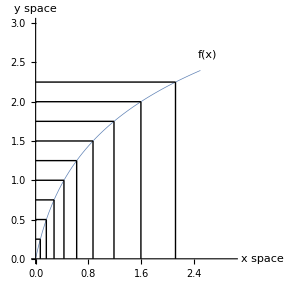

```mathematica
ClearAll[m1,m2,label1,label2,label3,option1];

m1=Table[{{(Exp[i*0.25]-1)/4,i*0.25},{(Exp[i*0.25]-1)/4,0}},{i,1,9}];
m2=Table[{{(Exp[i*0.25]-1)/4,i*0.25},{0,i*0.25}},{i,1,9}];

label1=DisplayForm[RowBox[{Style["x",FontFamily-> "Times",12,Italic],StyleForm[" space",FontFamily-> "Times",12]}]];

label2=DisplayForm[RowBox[{Style["y",FontFamily-> "Times",12, Italic],StyleForm[" space",FontFamily-> "Times",12]}]];

label3=DisplayForm[TraditionalForm[MakeBoxes[f[x],TraditionalForm]]];

option1={
AspectRatio->1,
Axes->True,
AxesLabel-> {label1,label2},
Frame-> False,
PlotRegion->{{0,1},{0,1}},
PlotRange-> {{0,3},{0,3}},
BaseStyle-> Directive[FontFamily-> "Times New Roman",12,Plain],
Ticks->False,
ImagePadding->{{5,5},{5,5}},
Epilog->{
 Line/@m1,
Line/@m2,
Text[label3,{2.6,2.6}],Map[Text[Round[4*#],{-0.1,#}]&,Table[i*0.25,{i,1,9}]],Map[Text[#⟦2⟧,{#⟦1⟧,-0.1}]&,Table[{(Exp[i*0.25]-1)/4,i},{i,1,9}]]}};

Plot[Log[1+4*x],{x,0,2.5},Evaluate[option1]]

SelectionMove[EvaluationNotebook[],Previous,Cell]
FrontEndExecute[FrontEndToken["OpenCloseGroup"]];
SelectionMove[EvaluationNotebook[],After,Cell]
```

Fig. Chapter.FigureCaption  The expanding dimensions in x space are mapped to dimensions of constant size in y space.

To transform the finite difference equation in x space to y space the second derivative of concentration with respect to distance, x, can be re-written as

∂/(∂x)(∂c)/(∂x)=((∂y)/(∂x))∂/(∂y)((∂y)/(∂x)(∂c)/(∂y))
=((∂y)/(∂x))((∂y)/(∂x)((∂^2 c)/(∂y^2))+(∂c)/(∂y)∂/(∂y)((∂y)/(∂x)))

Therefore Fick’s second law can be re-written as

(∂c)/(∂t)=D((∂y)/(∂x))((∂y)/(∂x)((∂^2 c)/(∂y^2))+(∂c)/(∂y)∂/(∂y)((∂y)/(∂x)))

As an example let’s consider the function

y=ln(1+a x)

where a is an adjustable expansion factor. The derivative of eqn (Chapter.EquationNumbered) is

(∂y)/(∂x)=a/(1+ a x)

rearranging eqn (Chapter.EquationNumbered) as x=f(y) gives

x=(exp(y)-1)/a

the derivative of which is

(∂x)/(∂y)=(exp(y))/a

that when inverted gives us derivative of y with respect to x expressed in terms of y

(∂y)/(∂x)=aexp(-y)

```mathematica
(*alternatively a rule replacement could have been used*)
Clear[a,y,x];

a/(1+a*x)/.x->(Exp[y]-1)/a
```

a ⅇ^-y

Therefore

∂/(∂y)((∂y)/(∂x))=∂/(∂y)aexp(-y)
=-a exp(-y)

Inserting these expressions into eqn (Chapter.EquationNumbered) gives

(∂c)/(∂t)=D a exp(-y)(a exp(-y)(∂^2 c)/(∂y^2)-aexp(-y)(∂c)/(∂y))
=D a^2 exp(-2y)((∂^2 c)/(∂y^2)-(∂c)/(∂y))

Equation (Chapter.EquationNumbered) can be discretized to give

(c(y,t+Δ t)-c(y,t))/Δt=D a^2 exp(-2y)(((c(y+Δ y,t)-c(y, t))-(c(y,t)-c(y-Δ y,t)))/(Δy)^2+(c(y+Δ y,t)-c(y-Δ y,t))/(2Δy))

After some re-arrangement we arrive at

c(y,t+Δ t)=DΔt/(Δy)^2 a^2 exp(-2y)(1-Δy/2)c(y+Δ y,t)+(1-2 DΔt/(Δy)^2 a^2 exp(-2y))c(y,t)+DΔt/(Δy)^2 a^2 exp(-2y)(1+Δy/2)c(y-Δ y, t)

Converting eqn (Chapter.EquationNumbered) to dimensionless form gives

(1+Δy/2)D_p c_(p-1)^k+(1-2 D_p)c_p^k+(1-Δy/2)D_p c_(p+1)^k=c_p^(k+1)

where

D_p=D^*exp(-2y)

and

D^*=DΔt/(Δy)^2 a^2

and subscript p is an index in y space. We can see from eqn (Chapter.EquationNumbered) that only small modifications are necessary to the method that we developed in §2.3. This time the model diffusion coefficient is distance dependant with its maximum value at y=0. The flux at the electrode surface in x space is

J(1,k) =-c^*D/Δx(c_2^k-c_1^k)

Equation (Chapter.EquationNumbered) can be discretized to give the value of Δy.

Δy=a/(1+ a x)Δx

At x = 0 this becomes

Δy=aΔx

This approximation will be sufficiently accurate only for very small values of Δ x, that will eventuate for large time steps and/or large values of D. Substituting eqn (Chapter.EquationNumbered) into (Chapter.EquationNumbered) gives the flux at the surface in terms of Δ y

J(1,k) =-c^*(a D)/Δy(c_2^k-c_1^k)

The two point approximation for the current is therefore

i(k) =n F A c^*(a D)/Δy(c_2^k-c_1^k)

At y=0, D_1=D^*therefore substituting Δy=(a(DΔt/D^*))^(1/2) and Δt=t_n/(n-1) into eqn (Chapter.EquationNumbered) gives the dimensionless current, i(k):

i(k) =(i(k))/(n F A c^*)(t_n/D)^(1/2)=(c_2^k-c_1^k)(D^*(n-1))^(1/2)

The maximum distance from the electrode surface that needs to be considered is x_max=6(D t_n)^(1/2)

y_max=ln(1+a x_max)=(m-1)Δ y

which in dimensionless form means that (y(p))_max=ln(1+6a). The maximum number of spacial grid points will therefore be

(m-1)=ln(1+6a)(DΔt/(Δy)^2)^(1/2)=(ln(1+6a))/a(D^*(n-1))^(1/2)

since y=(p-1)/(m-1)y_max eqn (Chapter.EquationNumbered) can be re-written as

D_p=D^*exp(-2(p-1)/(m-1)y_max)

To implement the expanding space grid we create a grid in which y space is divided into m-1 increments of size Δ y. The distance at any point y from the electrode surface is the (p+1)th increment. The important modification to the methods described in Chapter 2 comes with introduction of a distance dependant model diffusion coefficient. The stability criteria is now D_p<0.5. In the method below α=Δy/2.

```mathematica
ClearAll[variableExplicitSolve1];
(*procedural method in which α=Δy/2*)
variableExplicitSolve1[m_Integer,n_Integer,d_][yLim_,α_]:=
	Module[{p,k,x,c},
x=Exp[-2*(p-1)/(m-1)*yLim];
c =makeGrid[m,n];
		For[k=2,k≤n,k++,
			For[p=2,p≤m-1,p++,
				c⟦p,k⟧=(d*x*(1-α)*c⟦p+1,k-1⟧)+((1-2*d*x)*c⟦p,k-1⟧)+(d*x*(1+α)*c⟦p-1,k-1⟧)];];c];
```

The important parameter in all methods that employ an expanding grid is the expansion factor. Differences in the quality of results may arise from differences in the size of the expansion factor. When testing a simulation against a system for which there is a known analytical result the expansion factor can be adjusted to give the greatest accuracy in the results. When using expanding grids to simulate an unknown system it is not that straight forward so that several values of the expansion factor should be tested to evaluate the effect this parameter has on the variability of the simulation results. A functional alternative to the procedural method is shown below. In Chapter 2 the functional solver included a function to solve the concentrations at each time step.

```mathematica
ClearAll[𝔻,solveNext]

solveNext:=Flatten[{0.,ListCorrelate[{𝔻,(1- 2*𝔻),𝔻},#],1.}]&;
```

```mathematica
ClearAll[𝔻,conc,c]

conc =Array[c,6];
solveNext[conc]
```

{0.,𝔻 c[1]+(1-2 𝔻) c[2]+𝔻 c[3],𝔻 c[2]+(1-2 𝔻) c[3]+𝔻 c[4],𝔻 c[3]+(1-2 𝔻) c[4]+𝔻 c[5],𝔻 c[4]+(1-2 𝔻) c[5]+𝔻 c[6],1.}

We need to be able to update the kernel of ListCorrelate at each distance increment. We could try automatically incrementing, for example:

```mathematica
j=2;
ListCorrelate[{j++,1-2*j,j},conc]
```

{2 c[1]-5 c[2]+3 c[3],2 c[2]-5 c[3]+3 c[4],2 c[3]-5 c[4]+3 c[5],2 c[4]-5 c[5]+3 c[6]}

Unfortunately that doesn’t work however if the kernel is set as an Unevaluated function then it will be evaluated at each step:

```mathematica
j=2;
With[{kernel=Unevaluated[{j,1-2*j,j++}]},
ListCorrelate[kernel,conc]
]
```

{2 c[1]-3 c[2]+2 c[3],3 c[2]-5 c[3]+3 c[4],4 c[3]-7 c[4]+4 c[5],5 c[4]-9 c[5]+5 c[6]}

Therefore the solver for the expanding grid can be re-written as

```mathematica
ClearAll[solveNext2,𝔻,yLim,Δy];

solveNext2[start_,m_,𝔻_,yLim_,Δy_]:=Module[{p=2},
Flatten[{0.,
With[{kernel=Unevaluated[{𝔻*Exp[-2*(p-1)/(m-1)*yLim]*(1+Δy/2),(1- 2*𝔻*Exp[-2*(p-1)/(m-1)*yLim]),𝔻*Exp[-2*(p++-1)/(m-1)*yLim]*(1-Δy/2)}]},
ListCorrelate[kernel,start]],1.}]
];
```

```mathematica
ClearAll[p,m,c];

solveNext2[Array[c,6],m,𝔻,yLim,Δy]
```

{0.,ⅇ^(-(2 yLim)/(-1+m)) 𝔻 (1+Δy/2) c[1]+(1-2 ⅇ^(-(2 yLim)/(-1+m)) 𝔻) c[2]+ⅇ^(-(2 yLim)/(-1+m)) 𝔻 (1-Δy/2) c[3],ⅇ^(-(4 yLim)/(-1+m)) 𝔻 (1+Δy/2) c[2]+(1-2 ⅇ^(-(4 yLim)/(-1+m)) 𝔻) c[3]+ⅇ^(-(4 yLim)/(-1+m)) 𝔻 (1-Δy/2) c[4],ⅇ^(-(6 yLim)/(-1+m)) 𝔻 (1+Δy/2) c[3]+(1-2 ⅇ^(-(6 yLim)/(-1+m)) 𝔻) c[4]+ⅇ^(-(6 yLim)/(-1+m)) 𝔻 (1-Δy/2) c[5],ⅇ^(-(8 yLim)/(-1+m)) 𝔻 (1+Δy/2) c[4]+(1-2 ⅇ^(-(8 yLim)/(-1+m)) 𝔻) c[5]+ⅇ^(-(8 yLim)/(-1+m)) 𝔻 (1-Δy/2) c[6],1.}

An example of the full implementation of the explicit method with variable space grid is given in the accompanying notebook expandExplicit.nb.

For the fully implicit method we have

-(1+Δy/2)D_p c_(p-1)^(k+1)+(1+2 D_p)c_p^(k+1)-(1-Δy/2)D_p c_(p+1)^(k+1)=c_p^k

The series of equations to solve are therefore

(1+2 D_2)c_2^(k+1)-(1-Δy/2)D_2 c_3^(k+1)=c_2^k+(1+Δy/2)D_2 c_1^(k+1)
-(1+Δy/2)D_3 c_2^(k+1)+(1+2 D_3)c_3^(k+1)-(1-Δy/2)D_3 c_4^(k+1)=c_3^k
-(1+Δy/2)D_4 c_3^(k+1)+(1+2 D_4)c_4^(k+1)-(1-Δy/2)D_4 c_5^(k+1)=c_4^k
⋮
-(1+Δy/2)D_j c_(j-1)^(k+1)+(1+2 D_j)c_j^(k+1)-(1-Δy/2)D_j c_(j+1)^(k+1)=c_j^k
⋮
-(1+Δy/2)D_(m-1)c_(m-2)^(k+1)+(1+2 D_(m-1))c_(m-1)^(k+1)=c_(m-1)^k+(1-Δy/2)D_(m-1)c_m^(k+1)

where the reader is reminded that c_1^(k+1)and c_m^(k+1) are boundary values. When written in matrix form the system of equations shown in (Chapter.EquationNumbered) are

((1+2 D_2) | -(1-Δy/2)D_2 |   |   |   | 0
-(1+Δy/2)D_3 | (1+2 D_3) | -(1-Δy/2)D_3 |   |   |  
  | -(1+Δy/2)D_4 | (1+2 D_4) | -(1-Δy/2)D_4 |   |  
  |   | ⋱ | ⋱ | ⋱ |  
  |   |   | -(1+Δy/2)D_(m-2) | (1+2 D_(m-2)) | -(1-Δy/2)D_(m-2)
0 |   |   |   | -(1+Δy/2)D_(m-1) | (1+2 D_(m-1)))
·(c_2^(k+1)
c_3^(k+1)
⋮
c_j^(k+1)
⋮
c_(m-1)^(k+1))=(c_2^k+(1+Δy/2)D_2 c_1^(k+1)
c_3^k
⋮
c_j^k
⋮
c_(m-1)^k+(1-Δy/2)D_(m-1)c_m^(k+1))

Equation (Chapter.EquationNumbered) has the form A·u=b. Therefore to modify the fully implicit method for a potential step experiment to accommodate an expanding grid we simply redefine the diagonals in A and make a minor change to the vector b. In the procedure below α=Δ y/2 and 𝔻=a^2 D Δ t/(Δ y)^2.

```mathematica
ClearAll[makeVarDiagonals];

makeVarDiagonals[m_Integer,d_,yLim_,α_]:=
	Module[{x,y,z},
		x=Table[-d*Exp[-2*(j-1)/(m-1)*yLim]*(1+α),{j,3,m-1}];
		z=Table[-d*Exp[-2*(j-1)/(m-1)*yLim]*(1-α),{j,2,m-2}];
		y=Table[1+2*d*Exp[-2*(j-1)/(m-1)*yLim],{j,2,m-1}];

{x,y,z}]
```

An example of the full implementation of the implicit method with variable space grid is given in the accompanying notebook expandImplicit.nb.

### Chapter.Section.Subsection Expansion directly in x space

Rather than map the x coordinates into a new space an alternative is to work directly in x space and to incorporate the expansion into the model diffusion coefficient.

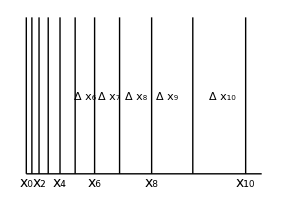

```mathematica
ClearAll[x,m1,label,label2];

m1=Table[{{(Exp[i*0.25]-1)/4,2},{(Exp[i*0.25]-1)/4,0}},{i,0,10}];

label[a_]:=DisplayForm[RowBox[{"Δ","",Subscript[Style["x",FontFamily-> "Times",Italic,14],a]}]];

label2[a_]:=DisplayForm[TraditionalForm[MakeBoxes[Style[Subscript[x, a],FontFamily-> "Times",14],TraditionalForm]]];

Graphics[{ 
Line[{{0,0},{3,0}}],
Line/@m1,
Text[label[10],{2.5,1.0}],
Text[label[9],{1.8,1.0}],
Text[label[8],{1.4,1.0}],
Text[label[7],{1.05,1.0}],
Text[label[6],{0.75,1.0}],
Map[Text[label2[#⟦2⟧],{#⟦1⟧,-0.1}]&,Table[{(Exp[i*0.25]-1)/4,i},{i,0,10,2}]]
}]

SelectionMove[EvaluationNotebook[],Previous,Cell]
FrontEndExecute[FrontEndToken["OpenCloseGroup"]];
SelectionMove[EvaluationNotebook[],After,Cell]
```

Fig. Chapter.FigureCaption  Expansion directly in x space.

The discretized version of Fick’s second law using the expanding grid can be derived from the Taylor expansion (see Appendix 1). If we were to take three points close together x_(j-1), x_j, and x_(j+1), and define the distance between these points as Δ x_(j+1)=x_(j+1)-x_j we can perform a Taylor expansion of a function of distance x as shown below. The forward, for, and backward, back, approximations to the derivative at x_j are obtained from:

```mathematica
ClearAll[for,j];

for=Series[f[Subscript[x, j]+Subscript[Δx, j+1]],{Subscript[Δx, j+1],0,2}]//Normal
```

f[x_j]+Δx_(1+j) f'[x_j]+1/2 Δx_(1+j)^2 f''[x_j]

```mathematica
ClearAll[back];

back=Series[f[Subscript[x, j]-Subscript[Δx, j]],{Subscript[Δx, j],0,2}]//Normal
```

f[x_j]-Δx_j f'[x_j]+1/2 Δx_j^2 f''[x_j]

The first derivative can be eliminated using Eliminate and the solution for the second derivative obtained.

```mathematica
ClearAll[expanding];

expanding=Eliminate[{f[Subscript[x, j]+Subscript[Δx, j+1]]==f[Subscript[x, j]]+Subscript[Δx, 1+j] f'[Subscript[x, j]]+1/2 Subscript[Δx, 1+j]^2 f''[Subscript[x, j]],f[Subscript[x, j]-Subscript[Δx, j]]==f[Subscript[x, j]]-Subscript[Δx, j] f'[Subscript[x, j]]+1/2 Subscript[Δx, j]^2 f''[Subscript[x, j]]},f'[Subscript[x, j]]]
```

2 f[x_j] Δx_j-2 f[x_j+Δx_(1+j)] Δx_j+2 f[x_j] Δx_(1+j)+Δx_j^2 Δx_(1+j) f''[x_j]+Δx_j Δx_(1+j)^2 f''[x_j]==2 f[x_j-Δx_j] Δx_(1+j)

The second derivative with respect to x is obtained by solving these two equations.

```mathematica
ClearAll[expanding2];

expanding2=Solve[expanding,f''[Subscript[x, j]]]//Simplify
```

{{f''[x_j]→(2 (f[x_j+Δx_(1+j)] Δx_j+f[x_j-Δx_j] Δx_(1+j)-f[x_j] (Δx_j+Δx_(1+j))))/(Δx_j Δx_(1+j) (Δx_j+Δx_(1+j)))}}

This result can be expressed in more familiar terms by using ReplaceAll to replace the function f with the concentration c. After rearranging this result the discretization of the second derivative with respect to x is

```mathematica
ClearAll[c,expanding3];

expanding3=expanding2/.{f[Subscript[x, j]+Subscript[Δx, j+1]]->Subscript[c, j+1],f[Subscript[x, j]]->Subscript[c, j],f[Subscript[x, j]-Subscript[Δx, j]]->Subscript[c, j-1]}//Simplify
```

{{f''[x_j]→(2 (c_(1+j) Δx_j+c_(-1+j) Δx_(1+j)-c_j (Δx_j+Δx_(1+j))))/(Δx_j Δx_(1+j) (Δx_j+Δx_(1+j)))}}

(∂^2 c)/(∂x^2)≅2((c_(j-1))/(Δ x_j(Δ x_(j+1)+Δ x_j))-c_j/(Δ x_(j+1)Δ x_j)+(c_(j+1))/(Δ x_(j+1)(Δ x_(j+1)+Δ x_j)))

We can check this result by making the distance increments equal

```mathematica
expanding3/.{Subscript[Δx, j]->Δx,Subscript[Δx, j+1]->Δx}//Simplify
```

{{f''[x_j]→(c_(-1+j)-2 c_j+c_(1+j))/Δx^2}}

For the fully implicit method the discretization of Fick’s second law becomes

c_j^(k+1)-c_j^k=D_j((Δ x_(j+1))/(Δ x_j)c_(j-1)^(k+1)-(Δ x_(j+1)+Δ x_j)/(Δ x_j)c_j^(k+1)+c_(j+1)^(k+1))

where

D_j=(2DΔt)/(Δ x_(j+1)(Δ x_(j+1)+Δ x_j))

Next step is to find an approximation for the flux at the electrode surface. The discretization of the first derivative with respect to x at j=1 is obtained in a similar fashion, this time eliminating the second derivative.

```mathematica
ClearAll[x,xi,f,taylorExp];

taylorExp=Series[f[x+Δx],{Δx,0,2}]
```

f[x]+f'[x] Δx+1/2 f''[x] Δx^2+O[Δx]^3

```mathematica
ClearAll[for1];

for1=Normal[taylorExp]/.Δx->Subscript[Δx, 2]
```

f[x]+Δx_2 f'[x]+1/2 Δx_2^2 f''[x]

```mathematica
ClearAll[for2];

for2=Normal[taylorExp]/.Δx:>(Subscript[Δx, 2]+Subscript[Δx, 3])
```

f[x]+(Δx_2+Δx_3) f'[x]+1/2 (Δx_2+Δx_3)^2 f''[x]

```mathematica
ClearAll[expanding4];

expanding4=Eliminate[{f[x+Subscript[Δx, 2]]==for1,f[x+(Subscript[Δx, 2]+Subscript[Δx, 3])]==for2},f''[x]]
```

f[x+Δx_2+Δx_3] Δx_2^2+2 f[x] Δx_2 Δx_3+f[x] Δx_3^2+Δx_2^2 Δx_3 f'[x]+Δx_2 Δx_3^2 f'[x]==f[x+Δx_2] (Δx_2^2+2 Δx_2 Δx_3+Δx_3^2)

Solving for the first derivatives gives

```mathematica
ClearAll[firstDeriv];

firstDeriv=Solve[expanding4,f'[x]]/.x-> Subscript[x, 1]//Simplify
```

{{f'[x_1]→(-f[x_1+Δx_2+Δx_3] Δx_2^2+f[x_1+Δx_2] (Δx_2+Δx_3)^2-f[x_1] Δx_3 (2 Δx_2+Δx_3))/(Δx_2 Δx_3 (Δx_2+Δx_3))}}

Substituting the concentration for the function at the first three points gives

```mathematica
firstDeriv=firstDeriv/.{f[Subscript[x, 1]+Subscript[Δx, 2]+Subscript[Δx, 3]]-> Subscript[c, 3],f[Subscript[x, 1]+Subscript[Δx, 2]]-> Subscript[c, 2],f[Subscript[x, 1]]-> Subscript[c, 1]}
```

{{f'[x_1]→(-c_3 Δx_2^2+c_2 (Δx_2+Δx_3)^2-c_1 Δx_3 (2 Δx_2+Δx_3))/(Δx_2 Δx_3 (Δx_2+Δx_3))}}

The three point approximation for the first derivative of concentration with respect to x at the electrode surface is therefore

(∂c)/(∂x)≅(-(Δ x_2)^2 c_3+(Δ x_2+Δ x_3)^2 c_2-Δ x_3(Δ x_3+2Δ x_2)c_1)/(Δ x_2 Δ x_3(Δ x_3+Δ x_2))

The flux at the electrode surface is

J(1,k)=-Dc^*((-(Δ x_2)^2 c_3^k+(Δ x_2+Δ x_3)^2 c_2^k-Δ x_3(Δ x_3+2Δ x_2)c_1^k)/(Δ x_2 Δ x_3(Δ x_3+Δ x_2)))

and the three point approximation for the current is

i(k)=n F A D c^*((-(Δ x_2)^2 c_3^k+(Δ x_2+Δ x_3)^2 c_2^k-Δ x_3(Δ x_3+2Δ x_2)c_1^k)/(Δ x_2 Δ x_3(Δ x_3+Δ x_2)))

The above approach is quite general but to implement it we now need to define how x expands. One method of grid expansion is described below. In this method the distance increments at j are

Δ x_(j+1)=x_(j+1)-x_j=a^(j-1)Δ x	for 1≤j≤m-1

Substituting this expression into eqn (Chapter.EquationNumbered) and re-arranging gives

c_j^k=-a D_j c_(j-1)^(k+1)+(1+(1+a)D_j)c_j^(k+1)-D_j c_(j+1)^(k+1)

where

D_j=D^*a^(3-2j)

and

D^*=(2DΔt)/((1+a)(Δx)^2)

The system of equations to solve are therefore

(1+(1+a)D_2)c_2^(k+1)-D_2 c_3^(k+1)=c_2^k+ a D_2 c_1^(k+1)
-a D_3 c_2^(k+1)+(1+(1+a)D_3)c_3^(k+1)-D_3 c_4^(k+1)=c_3^k
-a D_4 c_3^(k+1)+(1+(1+a)D_4)c_4^(k+1)-D_4 c_5^(k+1)=c_4^k
⋮
-a D_j c_(j-1)^(k+1)+(1+(1+a)D_j)c_j^(k+1)-D_j c_(j+1)^(k+1)=c_j^k
⋮
-a D_(m-1)c_(m-2)^(k+1)+(1+(1+a)D_(m-1))c_(m-1)^(k+1)=c_(m-1)^k+D_(m-1)c_m^(k+1)

where D_2=D^*/a and D_(m-1)=D^*/a^(2m-5). In matrix form the system of equations shown in (Chapter.EquationNumbered) is written as

((1+(1+a)D_2) | -D_2 |   |   |   | 0
-a D_3 | (1+(1+a)D_3) | -D_3 |   |   |  
  | -a D_4 | (1+(1+a)D_4) | -D_4 |   |  
  |   | ⋱ | ⋱ | ⋱ |  
  |   |   | -a D_(m-2) | (1+(1+a)D_(m-2)) | -D_(m-2)
0 |   |   |   | -a D_(m-1) | (1+(1+a)D_(m-1)))
·(c_2^(k+1)
c_3^(k+1)
⋮
c_j^(k+1)
⋮
c_(m-1)^(k+1))=(c_2^k+a D_2 c_1^(k+1)
c_3^k
⋮
c_j^k
⋮
c_(m-1)^k+a D_(m-1)c_m^(k+1))

This equation can be solved as described in §2.5. Combining eqns (Chapter.EquationNumbered) and (Chapter.EquationNumbered) gives the equation for the current.

```mathematica
ClearAll[a];

firstDeriv/.{Subscript[Δx, 2]-> Δx,Subscript[Δx, 3]->a*Δx}//Simplify
```

{{f'[x_1]→-(a (2+a) c_1-(1+a)^2 c_2+c_3)/(a (1+a) Δx)}}

i(k)=n F A c^*D/Δx((c_3^k-(1+a)^2 c_2^k+a(2+a)c_1^k)/(a(1+a)))

Substituting Δ x=(2D Δ t/(1+a)D^*)^(1/2) and Δ t=t_n/(n-1) into eqn (Chapter.EquationNumbered) gives the dimensionless current,

i(k) =(i(k))/(n F A c^*)(t_n/D)^(1/2)=(c_3^k-(1+a)^2 c_2^k+a(2+a)c_1^k)/(a(1+a))((D^*(1+a)(n-1))/2)^(1/2)

The maximum distance from the electrode surface that needs to be considered is x_max=6(D t_n)^(1/2). The maximum number of spacial grid points required can be obtained by solving

x_max=∑_(j=1)^(m-1) a^(j-1)Δx=6(D t_n)^(1/2)

Rearranging gives

∑_(j=1)^(m-1) a^(j-1)=6((D t_n)/(Δx)^2)^(1/2)

Rearranging eqn (Chapter.EquationNumbered) gives

(D^*(1+a)t_n)/(2Δt)=(D t_n)/(Δx)^2

therefore

(D^*(1+a)(n-1))/2=(DΔt(n-1))/(Δx)^2=(D t_n)/(Δx)^2

Substituting this into eqn (Chapter.EquationNumbered) gives the equation that must be solved for m to calculate them number of spacial grid points.

∑_(j=1)^(m-1) a^(j-1)=6((D^*(1+a)(n-1))/2)^(1/2)

The value of m can be obtained using either Solve or FindRoot.

Solve[∑_(j=1)^(m-1) a^(j-1)==6*√((𝔻*(1+a)*(n-1))/2),m,InverseFunctions→ True]

FindRoot[∑_(j=1)^(m-1) a^(j-1)==6*√((𝔻*(1+a)*(n-1))/2),{m,5},MaxIterations→ 20]

An example of the full implementation of the implicit method with an x expanding space grid is given in the accompanying notebook expandImplicit2.nb. An example of the explicit method with an expanding space grid is contained in the notebook expandExplicit2.nb.

## Chapter.Section Summary

This chapter demonstrated methods by which computations can be made more accurate and computational times can be reduced. All the numerical methods demonstrated thus far involve the solution of tridiagonal matrices using functions provided. In the following chapter the inner workings of one of these functions is examined and several methods of solving matrix equations are demonstrated and extended to cases where the problem to be solved has been set up in such a way that the diagonal elements of the tridiagonal matrix are each square matrices. This is typically the case when trying to solve problems involving coupled chemical reactions (Chapter 13).

## Further Reading

Britz, D. (1988). Digital Simulation in Electrochemistry, Springer-Verlag, Berlin.
Richtmyer, R. D. and Morton, K. W. (1967). Difference Methods for Initial Value Problems, (2nd edn) Wiley, New York.
Wolfram, S. (1999). The Mathematica Book, (4th edn) Cambridge University Press/Wolfram Media, New York/Champaign.